# HW 4 - ASTR 510

## Daniel George

## Q1

## b)

It was observed that number of iterations decreases monotonically with increase in ω. Therefore assuming ω lies between 0 and 1, the optimum value for ω is 1.

## c)

Number of poisson solver calls used for each run = 100

### Reading iterations and total time for each run

```mathematica
cData=Table[Extract[Import["C:\\Users\\dan7g\\Google Drive\\Acads\\ASTR510\\HW4\\qc-"<>s<>"-1.E-"<>ToString@n<>".dat"],{{-2,4},{-1,-2}}],{s,{"jacobi","gs","gsrb"}},{n,{3,6,9}}];
```

### Plots of iterations and averaged time vs grid size

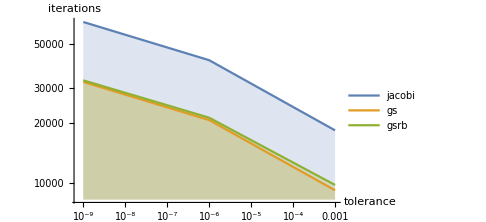
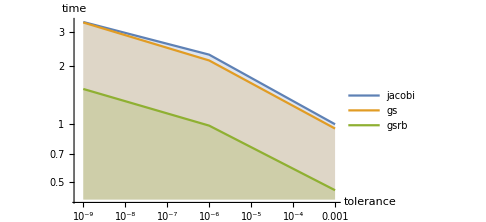

```mathematica
Column[Function[{x,y},ListLogLogPlot[Transpose[{10^Range[-3,-9,-3],cData[[#,All,x]]/100^(x-1)}]&/@Range[3],ImageSize->Medium,Joined->True,AxesLabel->{"tolerance",y},PlotLegends->{"jacobi","gs","gsrb"},Filling->Bottom]]@@@{{1,"iterations"},{2,"time"}}]
```

## d)

Minimum number of V-cycles for multigrid jacobi method is 28 for ω = 0.875 whereas Gauss-Seidel takes only 10 V-cycles. (Used bisection method manually to find the optimal value of ω)

## e)

The red black Gauss-Seidel smoother is the fastest with lowest number of V-cycles when Npre = Npost = 5. It is better to use more number of smoothing iterations that V-cycles because we can see that the total time taken decreases with more smoothing iterations.

## f)

## Iteration schemes

### Jacobi iteration

```mathematica
JAC=ϕ[n+1][j]==ϕ[n][j](1-w)+w/2(ϕ[n][j-1]+ϕ[n][j+1]-ρ[j]dx^2);
```

### Gauss-Seidel iteration

```mathematica
GS=ϕ[n+1][j]==1/2(ϕ[n+1][j-1]+ϕ[n][j+1]-ρ[j]dx^2);
```

## Stability analysis

### Trial solution for von Neumann

```mathematica
trial=ϕ[n_][j_]->ξ^n Exp[ I k j];
```

### Substituting it in the two schemes

Jacobi:

```mathematica
eqJAC=JAC/.trial//Simplify
```

ⅇ^(ⅈ (-1+j) k) ξ^n (w+ⅇ^(2 ⅈ k) w-2 ⅇ^(ⅈ k) (-1+w+ξ))==dx^2 w ρ[j]

Gauss-Seidel:

```mathematica
eqGS=GS/.trial//Simplify
```

ⅇ^(ⅈ (-1+j) k) ξ^n (ⅇ^(2 ⅈ k)+ξ-2 ⅇ^(ⅈ k) ξ)==dx^2 ρ[j]

### Solving for ξ assuming ρ = 0

Jacobi:

```mathematica
solJ=Solve[eqJAC[[1]]==0,ξ][[1,1]]//FullSimplify
```

ξ→1-w+w Cos[k]

Gauss-Seidel:

```mathematica
solGS=Solve[eqGS[[1]]==0,ξ][[1,1]]//FullSimplify
```

ξ→ⅇ^(2 ⅈ k)/(-1+2 ⅇ^(ⅈ k))

### Plots

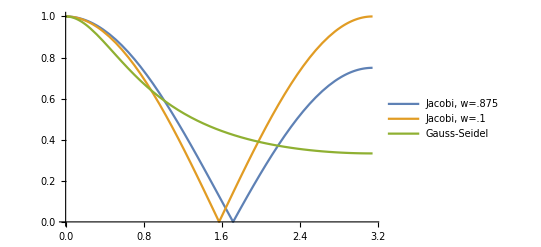

```mathematica
Plot[{Abs@ξ/.solJ/.w->.875,Abs@ξ/.solJ/.w->1,Abs@ξ/.solGS}//Evaluate,{k,0,Pi},PlotLegends->{"Jacobi, w=.875","Jacobi, w=.1","Gauss-Seidel"}]
```

Therefore we can see that Gauss-Seidel dampens the high frequency modes the fastest followed by the multigrid Jacobi method and the simple Jacobi method respectively.

## g)

Number of poisson solver calls used for each run = 100

### Reading V-cycles and total time for each run

```mathematica
gData=Table[Extract[Import["C:\\Users\\dan7g\\Google Drive\\Acads\\ASTR510\\HW4\\qf-"<>s<>"-"<>ToString@n<>".dat"],{{-2,4},{-1,-2}}],{s,{"jacobi","gs","gsrb"}},{n,2^Range[5,11]}];
```

### Plots of V-cycles and averaged time vs grid size

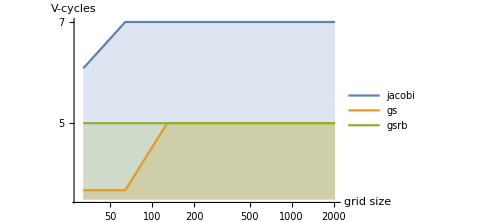
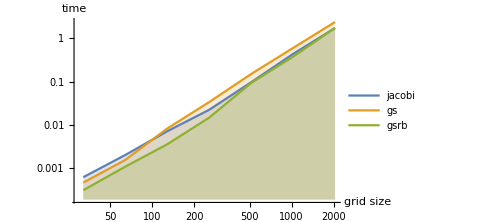

```mathematica
Column[Function[{x,y},ListLogLogPlot[Transpose[{2^Range[5,11],gData[[#,All,x]]/100^(x-1)}]&/@Range[3],ImageSize->Medium,Joined->True,AxesLabel->{"grid size",y},PlotLegends->{"jacobi","gs","gsrb"},Filling->Bottom]]@@@{{1,"V-cycles"},{2,"time"}}]
```

### Finding slope of best fit lines to the log-plots of time vs grid size for each method:

```mathematica
Transpose[{{"jacobi", "gs", "gsrb"},Fit[Log@#,{1,x},x][[2,1]]&/@(Transpose[{2^Range[5,11],gData[[#,;;,2]]/100}]&/@Range[3])}]//TableForm
```

jacobi | 1.9143
gs | 2.08326
gsrb | 2.10469

Therefore the Red Black Gauss-Seidel method scales the fastest asymptotically followed by the Gauss-Seidel and Jacobi methods respectively.

## Bash scripts

Each script generates a sequence of text files containing the information outputted to the terminal for each run.

## c)

```mathematica
sed-i'1s/.*/128 128/' inputs.dat
sed-i'8s/.*/1/' inputs.dat
sed-i "7s/.*/1 1/" inputs.dat
sed-i "10s/.*/100/" inputs.dat

echo "Starting runs for Jacobi"
sed-i "3s/.*/jacobi/" inputs.dat
for i in {1.E-3,1.E-6,1.E-9};
do
sed-i "5s/.*/$i/" inputs.dat
                ./poisson.exe>qc-jacobi-$i.dat
done

echo "Starting runs for Gauss-Seidel"
sed-i "3s/.*/gs/" inputs.dat
for i in {1.E-3,1.E-6,1.E-9};
do
sed-i "5s/.*/$i/" inputs.dat
                ./poisson.exe>qc-gs-$i.dat
done

echo "Starting runs for Red Black Gauss-Seidel"
sed-i "3s/.*/gsrb/" inputs.dat
for i in {1.E-3,1.E-6,1.E-9};
do
sed-i "5s/.*/$i/" inputs.dat
                ./poisson.exe>qc-gsrb-$i.dat
done

echo "Finished all runs"
```

## e)

```mathematica
sed -i '1s/.*/128/' inputs.dat
sed -i '8s/.*/.875/' inputs.dat
sed -i '5s/.*/1.E-6/' inputs.dat

echo "Starting runs for Jacobi"
sed -i "3s/.*/mg-jacobi/" inputs.dat
for i in `seq 0 5;
  do
    for j in `seq 0 5;
      do
                sed -i "7s/.*/$i $j/" inputs.dat
                ./poisson.exe > qe-jacobi-$i$j.dat
      done
  done

echo "Starting runs for Gauss-Seidel"
sed -i "3s/.*/mg-gs/" inputs.dat
for i in `seq 0 5;
  do
    for j in `seq 0 5;
      do
                sed -i "7s/.*/$i $j/" inputs.dat
                ./poisson.exe > qe-gs-$i$j.dat
      done
  done

echo "Starting runs for Red Black Gauss-Seidel"
sed -i "3s/.*/mg-gsrb/" inputs.dat
for i in `seq 0 5;
  do
    for j in `seq 0 5;
      do
                sed -i "7s/.*/$i $j/" inputs.dat
                ./poisson.exe > qe-gsrb-$i$j.dat
      done
  done

echo "Finished all runs"
```

## g)

```mathematica
sed-i'8s/.*/.875/' inputs.dat
sed-i "7s/.*/5 5/" inputs.dat
sed -i '5s/.*/1.E-6/' inputs.dat
echo "Starting runs for Jacobi"

sed-i "3s/.*/mg-jacobi/" inputs.dat
for i in {32,64,128,256,512,1024,2048};
do
sed-i "1s/.*/$i $i/" inputs.dat
                ./poisson.exe>qf-jacobi-$i.dat
done

echo "Starting runs for Gauss-Seidel"
sed-i "3s/.*/mg-gs/" inputs.dat
for i in {32,64,128,256,512,1024,2048};
do
sed-i "1s/.*/$i $i/" inputs.dat
                ./poisson.exe>qf-gs-$i.dat
done

echo "Starting runs for Red Black Gauss-Seidel"
sed-i "3s/.*/mg-gsrb/" inputs.dat
for i in {32,64,128,256,512,1024,2048};
do
sed-i "1s/.*/$i $i/" inputs.dat
                ./poisson.exe>qf-gsrb-$i.dat
done

echo "Finished all runs"
```